# Structure Characteristics Profiling using Eigenvector of Molecular Matrix

The 27th Annual Conference of the Japanese Society for Artificlal Intelligence, 2013, 2C1-1

## Prepare

## Program

```mathematica
(*Get["/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Matrix_operations.txt"]*)
```

```mathematica
Get["/Users/amanokou/gitsrc/MATH_SCRIPT/SCRIPTS/Matrix_operations.txt"]
```

## Problem

Reorder of matrix changes values of eigensystem.

```mathematica
test={
{0,1,0},
{1,0,2},
{0,2,0}}
```

{{0,1,0},{1,0,2},{0,2,0}}

```mathematica
Eigenvalues[test]
```

{-√5,√5,0}

```mathematica
Eigenvectors[test]//N//TableForm
```

0.5 | -1.11803 | 1.
0.5 | 1.11803 | 1.
-2. | 0. | 1.

```mathematica
testodr=Ordering[Eigenvalues[test]//N,All,Greater]
```

{2,3,1}

```mathematica
(testreo=matReOrder[test,testodr])//TableForm
```

0 | 2 | 1
2 | 0 | 0
1 | 0 | 0

```mathematica
Eigenvalues[testreo]
```

{-√5,√5,0}

```mathematica
Eigenvectors[testreo]//N//TableForm
```

-2.23607 | 2. | 1.
2.23607 | 2. | 1.
0. | -1. | 2.

提案: eigenvalueで行列をソート(matReOrder[])したのち、eigenvalueとeigenvectorを算出。eigenvalueは変わらない。

eigenIntensity : Eigensystem[test][[1]]*Eigensystem[test][[2]]

```mathematica
eigenIntensity[test]//N//TableForm
```

-1.11803 | 2.5 | -2.23607
1.11803 | 2.5 | 2.23607
0. | 0. | 0.

```mathematica
(test2=matReOrder[test,{2,3,1}])//TableForm
```

0 | 2 | 1
2 | 0 | 0
1 | 0 | 0

```mathematica
(test3=reOrder[test,{2,3,1}])//TableForm
```

1 | 0 | 2
0 | 2 | 0
0 | 1 | 0

```mathematica
(test4=mapReOrder[test,{2,3,1}])//TableForm
```

1 | 0 | 0
0 | 2 | 1
2 | 0 | 0

```mathematica
Eigenvalues[test2]
```

{-√5,√5,0}

```mathematica
Eigenvalues[test3]
```

{2,1,0}

```mathematica
Eigenvalues[test4]
```

{2,1,0}

```mathematica
Eigenvectors[test2]//N//TableForm
```

-2.23607 | 2. | 1.
2.23607 | 2. | 1.
0. | -1. | 2.

```mathematica
Eigenvectors[test3]//N//TableForm
```

2. | 2. | 1.
1. | 0. | 0.
-2. | 0. | 1.

```mathematica
Eigenvectors[test4]//N//TableForm
```

0. | 1. | 0.
1. | -2. | 2.
0. | -1. | 2.

```mathematica
Eigenvectors[test]//N//TableForm
```

0.5 | -1.11803 | 1.
0.5 | 1.11803 | 1.
-2. | 0. | 1.

```mathematica
mapReOrder[Eigenvectors[test]//N,{2,3,1}]//TableForm
```

-1.11803 | 1. | 0.5
1.11803 | 1. | 0.5
0. | 1. | -2.

```mathematica
matReOrder[Eigenvectors[test]//N,{2,3,1}]//TableForm
```

1.11803 | 1. | 0.5
0. | 1. | -2.
-1.11803 | 1. | 0.5

## Structure Characteristics Profiling using Eigenvector

```mathematica
un[x___]:=UndirectedEdge[x]
```

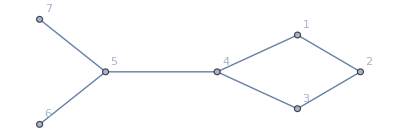

```mathematica
g=Graph[{un[1,2],un[2,3],un[3,4],un[4,5],un[5,6],un[5,7],un[1,4]},VertexLabels->"Name"]
```

```mathematica
(ad=AdjacencyMatrix[g]//Normal)//TableForm
```

0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0

```mathematica
va=Eigenvalues[ad]//N
```

{-2.23607,2.23607,-1.41421,1.41421,0.,0.,0.}

```mathematica
(reOrderEigen[ad]//N)[[1]]
```

{-2.23607,2.23607,-1.41421,1.41421,0.,0.,0.}

```mathematica
(reOrderEigen[ad]//N)[[2]]//TableForm
```

-0.894427 | -1.34164 | -0.447214 | -0.447214 | 1. | 1. | 1.
0.894427 | 1.34164 | 0.447214 | 0.447214 | 1. | 1. | 1.
-1.41421 | 0. | 1.41421 | 1.41421 | -2. | 1. | 1.
1.41421 | 0. | -1.41421 | -1.41421 | -2. | 1. | 1.
0. | 0. | 0. | 0. | 0. | -1. | 1.
1. | -1. | 0. | 1. | 0. | 0. | 0.
1. | -1. | 1. | 0. | 0. | 0. | 0.

```mathematica
(ei=Eigenvectors[ad]//N)//TableForm
```

-2.23607 | 2. | -2.23607 | 3. | -2.23607 | 1. | 1.
2.23607 | 2. | 2.23607 | 3. | 2.23607 | 1. | 1.
0.707107 | -1. | 0.707107 | 0. | -1.41421 | 1. | 1.
-0.707107 | -1. | -0.707107 | 0. | 1.41421 | 1. | 1.
0. | 1. | 0. | -1. | 0. | 0. | 1.
0. | 1. | 0. | -1. | 0. | 1. | 0.
-1. | 0. | 1. | 0. | 0. | 0. | 0.